# q q̄→μ μ in EW theory (SM ): UV divergences

CALCOLO DELLE DIVERGENZE UV VERTICI,BOX E SELF ENERGIES PER PROCESSO CONSIDERATO CON CARICHE SIMBOLICHE.
USO DI CALCRENCONST NEI CT. 
BOX->UV FINITE
VERTICI+CT->UV 
SELF+CT->UV
SELF+VERTICI+CT->UV FINITE

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;

process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
SetOptions[CalcFeynAmp,PaVeReduce->True];
```

## SM: Feynman rules

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2}
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3}
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3}
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3}
MASSES={MU->0,MU2->0,MM->0,MM2->0,S+T+U->0}
```

{QZLl→-1,QZUl→2/3,QZDl→-1/3,I3D→-1/2,I3L→-1/2,I3N→1/2,I3U→1/2}

{QZLr→-1,QZUr→2/3,QZDr→-1/3}

{QLl→-1,QUl→2/3,QDl→-1/3}

{QLr→-1,QUr→2/3,QDr→-1/3}

{MU→0,MU2→0,MM→0,MM2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-35.frm

running FORM...

ok

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
born = CalcFeynAmp[born1];
```

## Self Energies

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

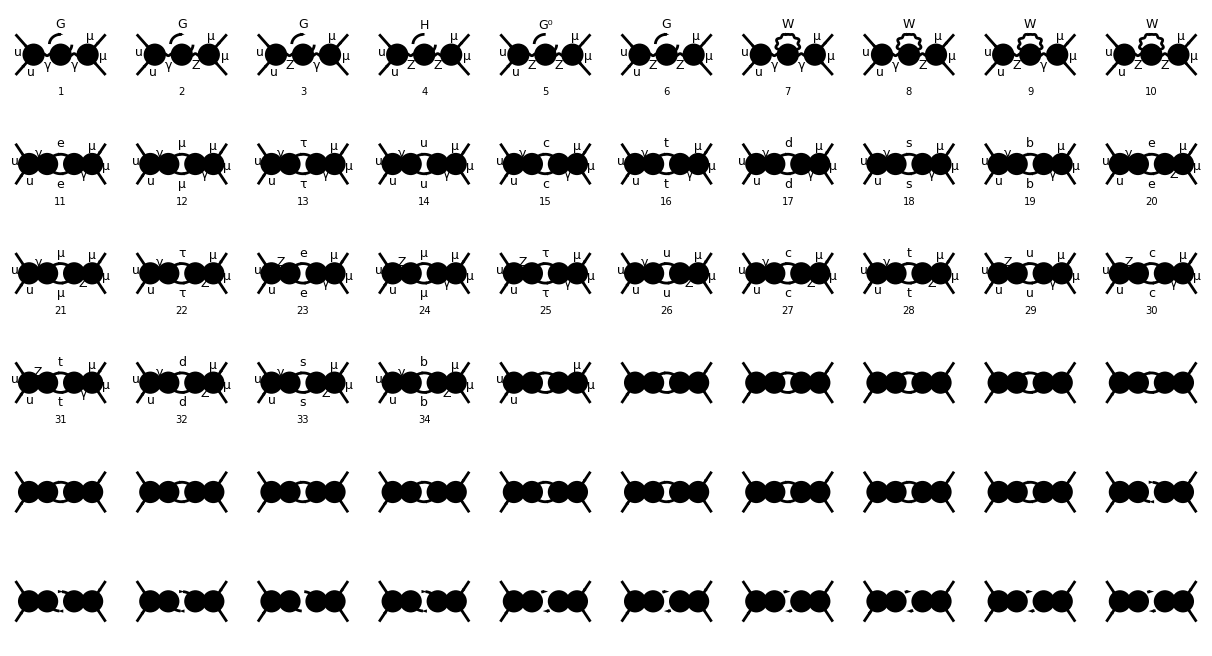

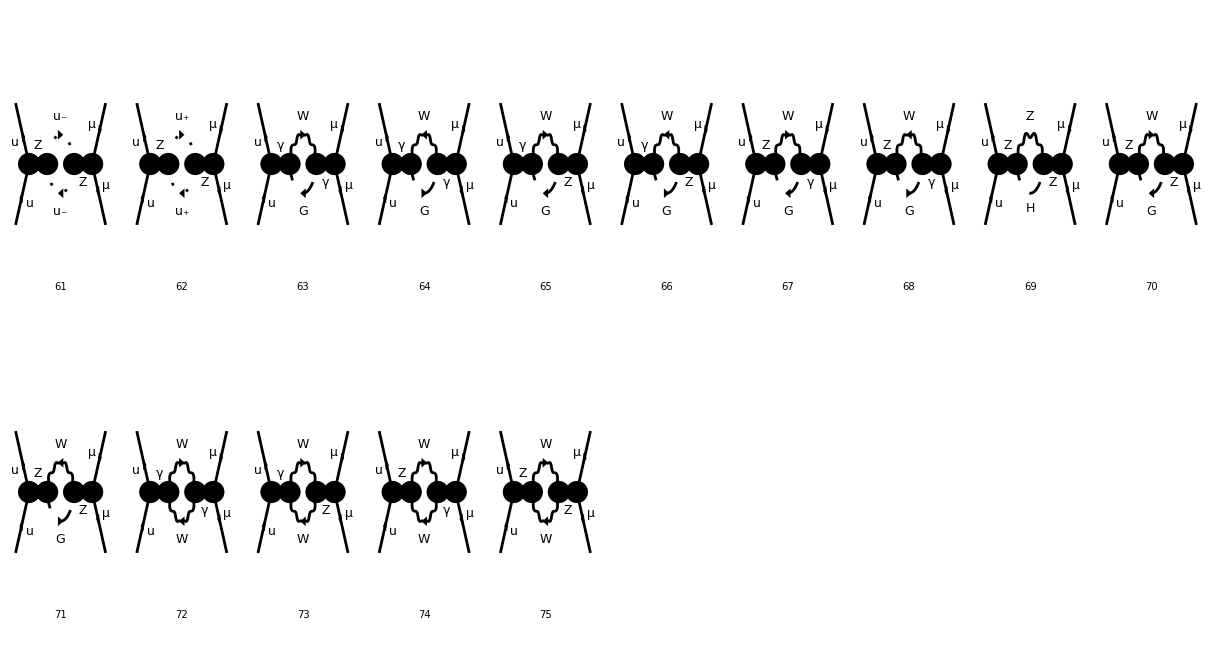

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20]
[21] | [22] | [23] | [24] | [25] | [26] | [27] | [28] | [29] | [30]
[31] | [32] | [33] | [34] | [35] | [36] | [37] | [38] | [39] | [40]
[41] | [42] | [43] | [44] | [45] | [46] | [47] | [48] | [49] | [50]
[51] | [52] | [53] | [54] | [55] | [56] | [57] | [58] | [59] | [60]),([61] | [62] | [63] | [64] | [65] | [66] | [67] | [68] | [69] | [70]
[71] | [72] | [73] | [74] | [75] | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null
Null | Null | Null | Null | Null | Null | Null | Null | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-35.frm

running FORM...

ok

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{10,6},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,656}]
selfff=CreateFeynAmp[ins2];
self = CalcFeynAmp[selfff];
```

```mathematica
selfdiv= UVDivergentPart[self[[1]]];
provaself = Unabbr[SSSSS*selfdiv] ;
```

## Vertices

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

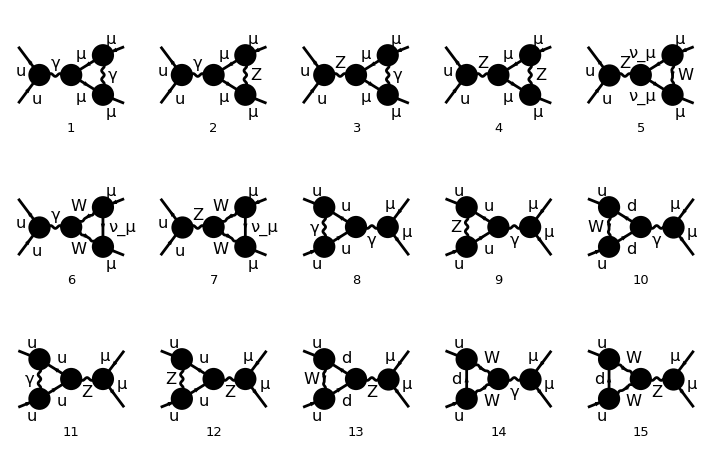

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-35.frm

running FORM...

ok

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
vert = CalcFeynAmp[verttt];
```

```mathematica
vertdiv = UVDivergentPart[vert[[1]]];
provavert = Unabbr[VVVVV *vertdiv] ;
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

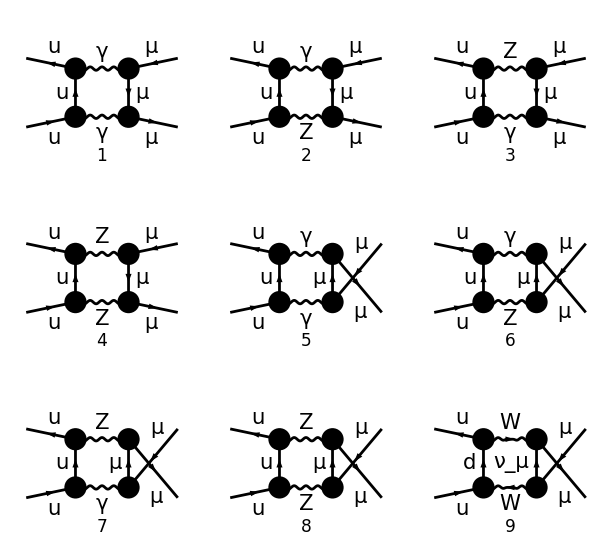

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-35.frm

running FORM...

$Aborted

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
box = CalcFeynAmp[box1];
```

### UV divergent part Boxes:

NO UV divergent part in these diagrams.

```mathematica
bboxUV=UVDivergentPart[box[[1]]] //Simplify
```

Alfa2 ((4 Divergence (CW2^2 (Sub1229+S (Sub1189+Sub522))+Sub526))/(CW2^2 S)+(-4 Divergence Sub507+(2 Divergence (Sub527+Sub582+S Sub530 U-F10 F9 (S+U)))/(S SW2^2 U)+(8 Divergence Sub1210-2 Divergence Sub542-(32 Divergence (MM2+MU2) Sub1190)/(U (-2 (MM2+MU2)+T+U)))/CW2)/T) Mat[SUN1]

```mathematica
Unabbr[bboxUV]//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr//.MASSES //SMSimplify
```

-1/(18 MW2^2 MZ2^2 S SW2^2 T (S+T) U (T+U))Alfa2 Divergence (S+T+U) Mat[SUNT[Col1,Col2]] (64 MZ2^4 SW2^4 (S (T-3 U)+T (T-2 U)) (T+U) ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+(64 MW2^4 (S (T-3 U)+T (T-2 U))-96 MW2^3 MZ2 (S (T-3 U)+T (T-2 U))-12 MW2 MZ2^3 (S (T-3 U)+T (T-2 U))+MZ2^4 (S (T-3 U)+T (T-2 U))+4 MW2^2 MZ2^2 (S (13 T-48 U)+13 T (T-2 U))) (T+U) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-256 MW2^4 S T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+768 MW2^3 MZ2 S T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-832 MW2^2 MZ2^2 S T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+384 MW2 MZ2^3 S T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-64 MZ2^4 S T U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-192 MW2^4 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+576 MW2^3 MZ2 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-624 MW2^2 MZ2^2 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+288 MW2 MZ2^3 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-48 MZ2^4 T^2 U ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-256 MW2^4 S U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+768 MW2^3 MZ2 S U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-832 MW2^2 MZ2^2 S U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+384 MW2 MZ2^3 S U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-64 MZ2^4 S U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-192 MW2^4 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+576 MW2^3 MZ2 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-624 MW2^2 MZ2^2 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+288 MW2 MZ2^3 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-48 MZ2^4 T U^2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-256 MW2^4 S T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+640 MW2^3 MZ2 S T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-528 MW2^2 MZ2^2 S T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+160 MW2 MZ2^3 S T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-16 MZ2^4 S T U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-192 MW2^4 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+480 MW2^3 MZ2 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-396 MW2^2 MZ2^2 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+120 MW2 MZ2^3 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-12 MZ2^4 T^2 U ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-256 MW2^4 S U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+640 MW2^3 MZ2 S U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-528 MW2^2 MZ2^2 S U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+160 MW2 MZ2^3 S U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-16 MZ2^4 S U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-192 MW2^4 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+480 MW2^3 MZ2 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-396 MW2^2 MZ2^2 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+120 MW2 MZ2^3 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))-12 MZ2^4 T U^2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2))+304 MW2^4 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-476 MW2^3 MZ2 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+290 MW2^2 MZ2^2 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-50 MW2 MZ2^3 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+4 MZ2^4 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+240 MW2^4 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-380 MW2^3 MZ2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+202 MW2^2 MZ2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-38 MW2 MZ2^3 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+3 MZ2^4 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+240 MW2^4 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-356 MW2^3 MZ2 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+230 MW2^2 MZ2^2 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-46 MW2 MZ2^3 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+4 MZ2^4 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+176 MW2^4 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-260 MW2^3 MZ2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+142 MW2^2 MZ2^2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-34 MW2 MZ2^3 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+3 MZ2^4 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+304 MW2^4 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-872 MW2^3 MZ2 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+896 MW2^2 MZ2^2 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-392 MW2 MZ2^3 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+64 MZ2^4 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+240 MW2^4 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-680 MW2^3 MZ2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+688 MW2^2 MZ2^2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-296 MW2 MZ2^3 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+48 MZ2^4 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+240 MW2^4 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-728 MW2^3 MZ2 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+800 MW2^2 MZ2^2 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-376 MW2 MZ2^3 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+64 MZ2^4 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+176 MW2^4 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-536 MW2^3 MZ2 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+592 MW2^2 MZ2^2 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))-280 MW2 MZ2^3 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+48 MZ2^4 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|6,k[1]|v3))+304 MW2^4 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-740 MW2^3 MZ2 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+584 MW2^2 MZ2^2 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-164 MW2 MZ2^3 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+16 MZ2^4 S T ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+240 MW2^4 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-580 MW2^3 MZ2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+452 MW2^2 MZ2^2 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-124 MW2 MZ2^3 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+12 MZ2^4 T^2 ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+240 MW2^4 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-604 MW2^3 MZ2 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+504 MW2^2 MZ2^2 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-156 MW2 MZ2^3 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+16 MZ2^4 S U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+176 MW2^4 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-444 MW2^3 MZ2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+372 MW2^2 MZ2^2 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-116 MW2 MZ2^3 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+12 MZ2^4 T U ((v̇ 1|6,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+304 MW2^4 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-1136 MW2^3 MZ2 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+1616 MW2^2 MZ2^2 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-1040 MW2 MZ2^3 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+256 MZ2^4 S T ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+240 MW2^4 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-880 MW2^3 MZ2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+1232 MW2^2 MZ2^2 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-784 MW2 MZ2^3 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+192 MZ2^4 T^2 ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+240 MW2^4 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-976 MW2^3 MZ2 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+1488 MW2^2 MZ2^2 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-1008 MW2 MZ2^3 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+256 MZ2^4 S U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+176 MW2^4 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-720 MW2^3 MZ2 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+1104 MW2^2 MZ2^2 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))-752 MW2 MZ2^3 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3))+192 MZ2^4 T U ((v̇ 1|7,k[3]|u2)) ((u̇ 4|7,k[1]|v3)))

```mathematica
%//.MASSES
```

0

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

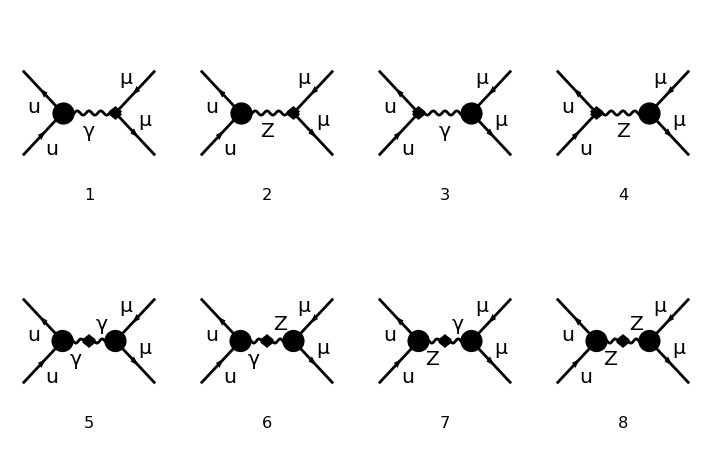

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

preparing FORM code in /home/arianna/Documenti/FormCalc-9.9/fc-amp-35.frm

running FORM...

ok

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
ct=CalcFeynAmp[counter];
counterterms = Unabbr[ct];
```

```mathematica
pv=Table[Unabbr[UVDivergentPart[CalcFeynAmp[Part[verttt,{i}]][[1]]]],{i,1,15}];
```

```mathematica
pvct=Table[Unabbr[CalcFeynAmp[Part[counter,{i}]][[1]]],{i,1,8}];
```

```mathematica
pse=Table[Unabbr[UVDivergentPart[CalcFeynAmp[Part[selfff,{i}]][[1]]]],{i,1,75}];
```

### Renormalization Constants (RC)

```mathematica
rc=CalcRenConst[counterterms];
```

```mathematica
ddd=Table[UVDivergentPart[rc[[1,i]]]//Simplify,{i,1,Length[rc[[1]]]}];
```

## SELF+VERTICES->UV finite

```mathematica
Table[ddd[[i,1]],{i,1,Length[ddd]}][[11]]
Position[pvct,%,Infinity];
Union[Table[%[[i,1]],{i,1,Length[%]}]]
```

dZfR1[2,2,2]

{1,2}

```mathematica
Table[ddd[[i,1]],{i,1,Length[ddd]}]
%[[4]]
Table[MemberQ[pvct[[i]],%,Infinity],{i,1,8}]
```

{dMWsq1,dMZsq1,dSW1,dZAA1,dZAZ1,dZe1,dZZA1,dZZZ1,dZfL1[2,2,2],dZfL1[3,1,1],dZfR1[2,2,2],dZfR1[3,1,1]}

dZAA1

{True,False,True,False,True,False,False,False}

```mathematica
Collect[ExpandSums[pvct[[1]]//.{dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd]//.Conjugate[x_]->x//.{QUl->QU,QLl->QL,QUr->QU,QLr->QL},{ WeylChain[__]}, FullSimplify]
```

(2 Alfa2 Divergence QL QU (CW2 QL^2+QZLr^2 SW2) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|u̇ 4)) ((u2|6|v3)))/CW2+(Alfa2 Divergence QL QU (CW2+2 CW2 QL^2 SW2+2 (I3L-QZLl SW2)^2) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(CW2 SW2)+(Alfa2 Divergence QL QU (CW2+2 CW2 QL^2 SW2+2 (I3L-QZLl SW2)^2) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(CW2 SW2)+(2 Alfa2 Divergence QL QU (CW2 QL^2+QZLr^2 SW2) Den[S,0] Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/CW2

```mathematica
ExpandSums[pvct[[1]]//.{dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd]//.Conjugate[x_]->x
tot1=Collect[VVVVV*( pv[[1]]+pv[[2]])+CCCCC*%//.MASSES,{ WeylChain[__],QZLl,QL,I3L}, FullSimplify]//.{CCCCC-VVVVV->0,-CCCCC+VVVVV->0}//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr//FullSimplify
```

-4 Alfa π Den[S,0] Mat[SUNT[Col1,Col2]] (-(Alfa Divergence QLl (CW2+2 CW2 QLl^2 SW2+2 (I3L-QZLl SW2)^2) (QUl ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+QUr ((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(8 CW2 π SW2)-(Alfa Divergence QLr (CW2 QLr^2+QZLr^2 SW2) (QUr ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+QUl ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))/(4 CW2 π)+(-(Alfa CW Divergence QLl (CW2+2 CW2 QLl^2 SW2+2 (I3L-QZLl SW2)^2) (QUl ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+QUr ((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(8 CW2 π SW2)-(Alfa CW Divergence QLr (CW2 QLr^2+QZLr^2 SW2) (QUr ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+QUl ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))/(4 CW2 π))/CW)

-(2 Alfa2 Divergence (CCCCC+2 CCCCC SW2-2 SW2 VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] (((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(3 SW2)

```mathematica
Collect[tot1,SW2,Simplify]//.{CCCCC-VVVVV->0,-CCCCC+VVVVV->0}
```

-(2 Alfa2 CCCCC Divergence Den[S,0] Mat[SUNT[Col1,Col2]] (((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(3 SW2)

```mathematica
ExpandSums[pvct[[2]]//.{dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd]//.Conjugate[x_]->x;
tot2=Collect[VVVVV*( pv[[3]]+pv[[4]]+pv[[5]]+pv[[7]])+CCCCC*%//.MASSES,{ WeylChain[__],QZLl,QL,I3L}, FullSimplify]//.{CCCCC-VVVVV->0,-CCCCC+VVVVV->0}//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr//Simplify
```

-1/(12 CW2 SW2^2)Alfa2 Divergence (CCCCC (-1+4 SW2^2)+(-1+6 CW2+2 SW2-4 SW2^2) VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((-3+4 SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+4 SW2 ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))

```mathematica
ExpandSums[pvct[[3]]//.  {dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd]//.Conjugate[x_]->x
tot3=Collect[VVVVV*( pv[[8]]+pv[[9]]+pv[[10]]+pv[[14]])+CCCCC*%//.MASSES,{ WeylChain[__],QZLl,QL,I3L}, FullSimplify]//.{CCCCC-VVVVV->0,-CCCCC+VVVVV->0}//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr//Simplify
```

-4 Alfa π Den[S,0] Mat[SUNT[Col1,Col2]] (-(Alfa Divergence QUr (CW2 QUr^2+QZUr^2 SW2) (QLr ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+QLl ((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(4 CW2 π)-(Alfa Divergence QUl (CW2+2 CW2 QUl^2 SW2+2 (I3U-QZUl SW2)^2) (QLl ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+QLr ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))/(8 CW2 π SW2)+(-(Alfa CW Divergence QUr (CW2 QUr^2+QZUr^2 SW2) (QLr ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+QLl ((v̇ 1|7|v3)) ((u̇ 4|6|u2))))/(4 CW2 π)-(Alfa CW Divergence QUl (CW2+2 CW2 QUl^2 SW2+2 (I3U-QZUl SW2)^2) (QLl ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+QLr ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))/(8 CW2 π SW2))/CW)

-1/(27 CW2 SW2)Alfa2 Divergence (CCCCC ((3-4 SW2)^2+2 CW2 (9+8 SW2))-((3-4 SW2)^2+8 CW2 (9+2 SW2)) VVVVV) Den[S,0] Mat[SUNT[Col1,Col2]] (((v̇ 1|6|u̇ 4)) ((u2|7|v3))+((v̇ 1|6|v3)) ((u̇ 4|7|u2)))

```mathematica
ExpandSums[pvct[[4]]//.  {dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd]//.Conjugate[x_]->x;
tot4=Collect[VVVVV*( pv[[11]]+pv[[12]]+pv[[13]]+pv[[15]])+CCCCC*%//.MASSES,{ WeylChain[__],QZLl,QL,I3L}, FullSimplify]//.{CCCCC-VVVVV->0,-CCCCC+VVVVV->0}//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr//Simplify
```

-1/(216 CW2^2 SW2^2)Alfa2 Divergence (CCCCC (-3+4 SW2) ((3-4 SW2)^2+2 CW2 (9+8 SW2))+(324 CW2^2-(-3+4 SW2)^3+CW2 (-54+84 SW2-64 SW2^2)) VVVVV) Den[S,MZ2] Mat[SUNT[Col1,Col2]] ((-1+2 SW2) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+2 SW2 ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))

```mathematica
Collect[tot1+tot2+tot3+tot4//.CCCCC->1//.VVVVV->1,{ WeylChain[__]},Simplify]
```

(2 Alfa2 Divergence (5 SW2 Den[S,0]+(3-5 SW2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(3 SW2^2)+(4 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)+(2 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

```mathematica
Plus@@ExpandSums[pvct[[5;;8]]//.{dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ddd];
Collect[SSSSS*psel+CCCCC*%//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr,{ WeylChain[__],QZLl,QL,I3L},Simplify]//. MASSES //.{CCCCC->1,SSSSS->1}//SMFullSimplify
```

0

```mathematica
psel=Plus@@pse[[1;;75]];
```

```mathematica
Plus@@ExpandSums[pvct[[1;;8]]//.{dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ddd];
Collect[Collect[SSSSS*psel+CCCCC*%//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr,{ WeylChain[__],QZLl,QL,I3L},Simplify]//. MASSES //.{CCCCC->1,SSSSS->1}//SMFullSimplify,{ WeylChain[__],QZLl,QL,I3L},Simplify]
```

(2 Alfa2 Divergence (-5 MZ2 SW2 Den[S,0]+(-5 MW2+2 MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(3 MZ2 SW2^2)-(4 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)-(2 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

## Vertici

```mathematica
ctvert=CCCCC*ExpandSums[counterterms[[1]]//.  {dMZsq1->0,dMWsq1->0,dSW1->0,dZAA1->0, dZZZ1->0, dZZA1->0, dZe1->0, dZAZ1->0}//.ddd];
```

```mathematica
uvvert1 = Collect[ provavert+ctvert//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr, WeylChain[__], FullSimplify];
```

```mathematica
uvvert2= ExpandSums[ uvvert1 ] //.{CCCCC->1,VVVVV->1}//. MASSES //SMSimplify;
```

```mathematica
uvvert3= Collect[ uvvert2 , WeylChain[__], SMSimplify]
```

(2 Alfa2 Divergence (5 MZ2 SW2 Den[S,0]+(5 MW2-2 MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(3 MZ2 SW2^2)+(4 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)+(2 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

## Self-energies

```mathematica
ctself=CCCCC*ExpandSums[counterterms[[1]]//.{dZfL1[__]->0,Conjugate[dZfL1[__]]->0,dZfR1[__]->0,Conjugate[dZfR1[__]]->0}//.ddd] ;
```

```mathematica
uvself1=Collect[ provaself+ctself//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr, WeylChain[__], Simplify];
```

```mathematica
uvself2=ExpandSums[ uvself1 ] //.{CCCCC->1,SSSSS->1}//. MASSES   //SMFullSimplify;
```

```mathematica
uvself3=Collect[ uvself2, WeylChain[__], SMSimplify]
```

(2 Alfa2 Divergence (-5 MZ2 SW2 Den[S,0]+(-5 MW2+2 MZ2) Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|u̇ 4)) ((u2|7|v3)))/(3 MZ2 SW2^2)-(4 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|7|v3)) ((u̇ 4|6|u2)))/(3 SW2)-(2 Alfa2 Divergence (Den[S,0]-Den[S,MZ2]) Mat[SUNT[Col1,Col2]] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))/SW2

## Vertici+Self

```mathematica
ct1=ExpandSums[counterterms[[1]]//.ddd] ;
```

```mathematica
c2=Collect[ provavert+provaself+ct1, WeylChain[__], Simplify];
```

$Aborted

```mathematica
c3=ExpandSums[ c2 ] //.{TTTTTT->1,SSSSS->1,VVVVV->1}//.CHARGESZl//.CHARGESZr//.CHARGESphl//.CHARGESphr//. MASSES   //SMSimplify
```

1/(108 MW2^2 MZ2^2 S SW2^2)Alfa2 Divergence (MW2-CW2 MZ2) Mat[SUNT[Col1,Col2]] (-288 MW2^2 MZ2 S SW2 Den[S,0] ((v̇ 1|7|v3)) ((u̇ 4|6|u2))+Den[S,MZ2]^2 (192 MZ2^2 (ME2 (3 MW2-4 MZ2)+ML2 (3 MW2-4 MZ2)-(MB2+MD2+MS2) MZ2) S SW2^2 ((v̇ 1|7|u̇ 4)) ((u2|6|v3))+3 (4 MW2-MZ2) (MH2^2 MZ2^2+MZ2^4-2 MZ2^3 S+MZ2^2 (26 MB2+18 MC2+26 MD2+6 ME2+6 ML2+26 MS2+18 MT2-24 MW2-81 S) S-92 MW2^2 S^2-2 MH2 MZ2^2 (MZ2+S)+4 MW2 MZ2 S (-4 MB2-4 MD2-4 MS2+12 MW2+41 S)) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))-4 MZ2 SW2 ((3 MH2^2 MZ2^2+3 MZ2^4-6 MZ2^3 S+MZ2^2 (78 MB2-10 MC2+78 MD2+42 ME2+42 ML2+78 MS2-10 MT2-72 MW2-225 S) S-6 MH2 MZ2^2 (MZ2+S)-4 MW2^2 S (16 MC2+16 MT2+69 S)+4 MW2 MZ2 S (-12 MB2+32 MC2-12 MD2-12 ME2-12 ML2-12 MS2+32 MT2+36 MW2+123 S)) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-12 (MB2+MD2+MS2) (4 MW2-MZ2) MZ2 S ((v̇ 1|6|v3)) ((u̇ 4|7|u2))))-4 Den[S,MZ2] (3 S (-20 MW2^3+14 MW2^2 MZ2+6 MW2 MZ2^2-3 MZ2^3+24 ME2 MZ2^2 SW2^2+6 MW2 MZ2 (-4 ML2 MW2+4 MW2^2+ML2 MZ2+5 MW2 MZ2+ME2 (-4 MW2+MZ2)) SW2 Den[S,0]) ((v̇ 1|6|u̇ 4)) ((u2|7|v3))+2 MZ2 SW2 ((-2 MW2^2 (26 MZ2+37 S)+MW2 (-36 ME2 S+MZ2^2 (50+36 SW2)+MZ2 S (109+72 SW2))+MZ2 (36 ME2 S+MZ2^2 (-25+18 SW2-36 SW2^2)-2 MZ2 S (25-18 SW2+36 SW2^2))+24 MW2^2 (MW2+2 MZ2) S Den[S,0]) ((v̇ 1|7|v3)) ((u̇ 4|6|u2))-3 (3 ME2+3 ML2-MW2) MW2 (4 MW2-MZ2) S Den[S,0] ((v̇ 1|6|v3)) ((u̇ 4|7|u2)))))

```mathematica
c3//SMFullSimplify
```

0